## Floquet Engineering of Triplefold Fermions

```mathematica
$PrePrint = StandardForm
```

StandardForm

```mathematica
H3f[kx_,ky_,kz_]:= {{0,Exp[I phi]kx, Exp[-I phi] ky},{Exp[-I phi]kx,0,Exp[I phi]kz},{Exp[I phi]ky,Exp[-I phi]kz,0}};
```

```mathematica
Eigs3f[kx_,ky_,kz_]:=Sort[Eigenvalues[N[H3f[kx,ky,kz]]]];
Eigs3ffn1[kx_,ky_,kz_]:=Eigs3f[kx,ky,kz][[1]];

Eigs3ffn2[kx_,ky_,kz_]:=Eigs3f[kx,ky,kz][[2]];

Eigs3ffn3[kx_,ky_,kz_]:=Eigs3f[kx,ky,kz][[3]];
```

```mathematica
Plot3D[{Eigs3ffn1[0,ky,kz],Eigs3ffn2[0,ky,kz],Eigs3ffn3[0,ky,kz]},{ky,-Pi,Pi},{kz,-Pi,Pi},PlotRange->All,Mesh->None,PlotStyle->{Directive[Opacity[0.4],Blue],
Directive[Opacity[0.4],Red],Directive[Opacity[0.4],Green]},RegionFunction->Function[{kx,ky,z},kx^2+ky^2<=2],AspectRatio->1]
```

-Graphics3D-

```mathematica
phi=Pi/6
```

π/6

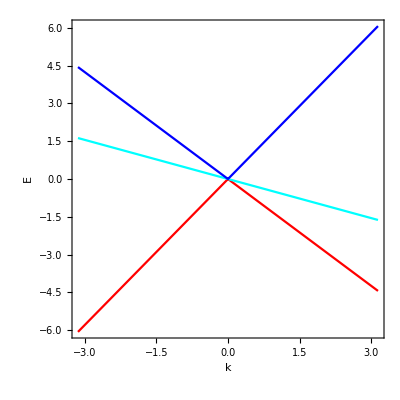

```mathematica
Show[Plot[{Eigs3ffn1[k,k,k],Eigs3ffn2[k,k,k],Eigs3ffn3[k,k,k]},{k,-Pi,Pi},PlotStyle->{Red,Cyan,Blue},AspectRatio->1],Frame->True,LabelStyle->Directive[Bold,Black,20],FrameLabel->{Style["k",Black,Bold,Italic,26],Style["E",Black,Bold,Italic,26]}]
```

```mathematica
Eigs3f[0.3,0.3,0.3]
```

{-0.3,-0.3,0.6}

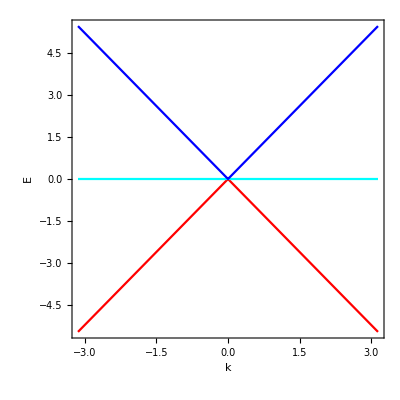

```mathematica
Show[Plot[{Eigs3ffn1[k,k,k],Eigs3ffn2[k,k,k],Eigs3ffn3[k,k,k]},{k,-Pi,Pi},PlotStyle->{Red,Cyan,Blue},AspectRatio->1],Frame->True,LabelStyle->Directive[Bold,Black,20],FrameLabel->{Style["k",Black,Bold,Italic,26],Style["E",Black,Bold,Italic,26]}]
```

```mathematica
Export["/Users/aneekphys/Documents/BCL plots/multifold_phi_pi_by_6.pdf",%]
```

/Users/aneekphys/Documents/BCL plots/multifold_phi_pi_by_6.pdf

```mathematica
Export["/Users/aneekphys/Documents/BCL plots/multifold_phi_pi_by_12.pdf",%]
```

/Users/aneekphys/Documents/BCL plots/multifold_phi_pi_by_12.pdf

## BCL

```mathematica
Ax =A0( r Cos[η w t - α] + Cos[w t])(* r controls the relative strength between the two frequencies*)
Ay =A0( - r Sin[η w t - α] + Sin[w t])
```

A0 (Cos[t w]+r Cos[α-t w η])

A0 (Sin[t w]+r Sin[α-t w η])

```mathematica
TeXForm[Ay/.{w->omega}]
```

r \sin (\alpha -\eta  \omega  t)+\sin (\omega  t)

### Plotting The BCL lights

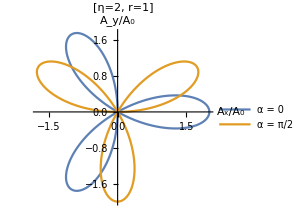

```mathematica
ParametricPlot[{{Ax/A0/.{η->2,α->0,w->1,r->1},Ay/A0/.{η->2,α->0,w->1,r->1}},{Ax/A0/.{η->2,α->Pi/2,w->1,r->1},Ay/A0/.{η->2,α->Pi/2,w->1,r->1}}},{t,0,2 Pi},AxesLabel->{"A_x/A_0","A_y/A_0"},PlotLegends->{"α = 0","α = π/2"},PlotLabel->"[η=2, r=1]"](* r=1 *)
```

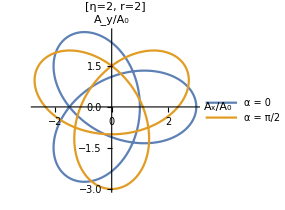

```mathematica
ParametricPlot[{{Ax/A0/.{η->2,α->0,w->1,r->2},Ay/A0/.{η->2,α->0,w->1,r->2}},{Ax/A0/.{η->2,α->Pi/2,w->1,r->2},Ay/A0/.{η->2,α->Pi/2,w->1,r->2}}},{t,0,2 Pi},AxesLabel->{"A_x/A_0","A_y/A_0"},PlotLegends->{"α = 0","α = π/2"},PlotLabel->"[η=2, r=2]"](* r=2 *) (*see the interesting pattern when r is not equal to 1*)
```

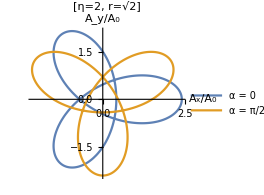

```mathematica
ParametricPlot[{{Ax/A0/.{η->2,α->0,w->1,r->Sqrt[2]},Ay/A0/.{η->2,α->0,w->1,r->Sqrt[2]}},{Ax/A0/.{η->2,α->Pi/2,w->1,r->Sqrt[2]},Ay/A0/.{η->2,α->Pi/2,w->1,r->Sqrt[2]}}},{t,0,2 Pi},AxesLabel->{"A_x/A_0","A_y/A_0"},PlotLegends->{"α = 0","α = π/2"},PlotLabel->"[η=2, r=√2]"](* r=Sqrt[2] *)
```

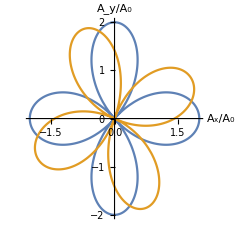

```mathematica
ParametricPlot[{{Ax/A0/.{η->3,α->0,w->1,r->1},Ay/A0/.{η->3,α->0,w->1,r->1}},{Ax/A0/.{η->3,α->Pi/2,w->1,r->1},Ay/A0/.{η->3,α->Pi/2,w->1,r->1}}},{t,0,2 Pi},AxesLabel->{"A_x/A_0","A_y/A_0"}](* r=1 *)
```

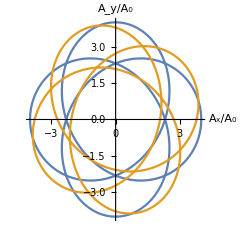

```mathematica
ParametricPlot[{{Ax/A0/.{η->3,α->0,w->1,r->3},Ay/A0/.{η->3,α->0,w->1,r->3}},{Ax/A0/.{η->3,α->Pi/2,w->1,r->3},Ay/A0/.{η->3,α->Pi/2,w->1,r->3}}},{t,0,2 Pi},AxesLabel->{"A_x/A_0","A_y/A_0"}](* r=3 *)
```

```mathematica
(*The initial Hamiltonian*)
```

```mathematica
H3f[kx,ky,kz]//MatrixForm
```

(0 | ⅇ^(ⅈ phi) kx | ⅇ^(-ⅈ phi) ky
ⅇ^(-ⅈ phi) kx | 0 | ⅇ^(ⅈ phi) kz
ⅇ^(ⅈ phi) ky | ⅇ^(-ⅈ phi) kz | 0)

```mathematica
TeXForm[H3f[Subscript[k, x],Subscript[k, y],Subscript[k, z]]]
```

\left(
\begin{array}{ccc}
 0 & e^{i \phi } k_x & e^{-i \phi } k_y \\
 e^{-i \phi } k_x & 0 & e^{i \phi } k_z \\
 e^{i \phi } k_y & e^{-i \phi } k_z & 0 \\
\end{array}
\right)

```mathematica
(*Hamiltonian after Pierls substitution*)
```

```mathematica
H3ftime = H3f[kx+Ax,ky+Ay,kz];
```

```mathematica
$Assumptions := {η ∈ Integers};
```

```mathematica
(*Calculating Fourier components to use Floquet theory*)
```

```mathematica
HP1 =w/(2 Pi) Integrate[H3ftime Exp[-I w t],{t,0, 2 Pi/w}]//FullSimplify
HM1 =w/(2 Pi) Integrate[H3ftime Exp[+I w t],{t,0, 2 Pi/w}]//FullSimplify
```

{{0,1/2 A0 ⅇ^(ⅈ phi),-1/2 ⅈ A0 ⅇ^(-ⅈ phi)},{1/2 A0 ⅇ^(-ⅈ phi),0,0},{1/2 A0 (-ⅈ Cos[phi]+Sin[phi]),0,0}}

{{0,1/2 A0 ⅇ^(ⅈ phi),1/2 A0 (ⅈ Cos[phi]+Sin[phi])},{1/2 A0 ⅇ^(-ⅈ phi),0,0},{1/2 ⅈ A0 ⅇ^(ⅈ phi),0,0}}

```mathematica
TeXForm[HM1]
```

\left(
\begin{array}{ccc}
 0 & \frac{e^{i \phi }}{2} & \frac{1}{2} (\sin
   (\phi )+i \cos (\phi )) \\
 \frac{e^{-i \phi }}{2} & 0 & 0 \\
 \frac{1}{2} i e^{i \phi } & 0 & 0 \\
\end{array}
\right)

```mathematica
HPeta =w/(2 Pi) Integrate[H3ftime Exp[-I η w t],{t,0, 2 Pi/w}]//FullSimplify
HMeta=w/(2 Pi) Integrate[H3ftime Exp[+I η w t],{t,0, 2 Pi/w}]//FullSimplify
```

{{0,1/2 A0 ⅇ^(ⅈ (phi-α)) r,1/2 ⅈ A0 ⅇ^(-ⅈ (phi+α)) r},{1/2 A0 ⅇ^(-ⅈ (phi+α)) r,0,0},{1/2 ⅈ A0 ⅇ^(ⅈ (phi-α)) r,0,0}}

{{0,1/2 A0 ⅇ^(ⅈ (phi+α)) r,-1/2 ⅈ A0 ⅇ^(-ⅈ (phi-α)) r},{1/2 A0 ⅇ^(-ⅈ (phi-α)) r,0,0},{-1/2 ⅈ A0 ⅇ^(ⅈ (phi+α)) r,0,0}}

```mathematica
HP1//MatrixForm
```

(0 | 1/2 A0 ⅇ^(ⅈ phi) | -1/2 ⅈ A0 ⅇ^(-ⅈ phi)
1/2 A0 ⅇ^(-ⅈ phi) | 0 | 0
1/2 A0 (-ⅈ Cos[phi]+Sin[phi]) | 0 | 0)

```mathematica
HM1 //MatrixForm
```

(0 | 1/2 A0 ⅇ^(ⅈ phi) | 1/2 A0 (ⅈ Cos[phi]+Sin[phi])
1/2 A0 ⅇ^(-ⅈ phi) | 0 | 0
1/2 ⅈ A0 ⅇ^(ⅈ phi) | 0 | 0)

```mathematica
HPeta //MatrixForm
```

(0 | 1/2 A0 ⅇ^(ⅈ (phi-α)) r | 1/2 ⅈ A0 ⅇ^(-ⅈ (phi+α)) r
1/2 A0 ⅇ^(-ⅈ (phi+α)) r | 0 | 0
1/2 ⅈ A0 ⅇ^(ⅈ (phi-α)) r | 0 | 0)

```mathematica
HMeta //MatrixForm
```

(0 | 1/2 A0 ⅇ^(ⅈ (phi+α)) r | -1/2 ⅈ A0 ⅇ^(-ⅈ (phi-α)) r
1/2 A0 ⅇ^(-ⅈ (phi-α)) r | 0 | 0
-1/2 ⅈ A0 ⅇ^(ⅈ (phi+α)) r | 0 | 0)

```mathematica
(*Effective Hamiltonian using Floquet theory*)
```

```mathematica
Heff = H3f[kx,ky,kz] + 1/w(HP1.HM1-HM1.HP1) + 1/(w η)(HPeta.HMeta-HMeta.HPeta)-1/w(-1/2(H3f[kx,ky,kz].HP1-HP1.H3f[kx,ky,kz])+1/2(H3f[kx,ky,kz].HM1-HM1.H3f[kx,ky,kz]))-1/(η w)(-1/2(H3f[kx,ky,kz].HPeta-HPeta.H3f[kx,ky,kz])+1/2(H3f[kx,ky,kz].HMeta-HMeta.H3f[kx,ky,kz]))//FullSimplify
```

{{0,ⅇ^(ⅈ phi) kx+(ⅈ A0 ⅇ^(-2 ⅈ phi) kz (η-r Cos[α]))/(2 w η),(ⅇ^(-ⅈ (phi+α)) (A0 ⅇ^(3 ⅈ phi) (-1+ⅇ^(2 ⅈ α)) kz r+4 ⅇ^(ⅈ α) ky w η))/(4 w η)},{(ⅇ^(-ⅈ (phi+α)) (2 ⅇ^(ⅈ α) kx w η+A0 kz (η-r Cos[α]) (-ⅈ Cos[3 phi+α]+Sin[3 phi+α])))/(2 w η),0,ⅇ^(ⅈ phi) kz+(ⅈ A0 ⅇ^(-2 ⅈ phi) (-A0 r^2+A0 η-kx η+kx r Cos[α]+ky r Sin[α]))/(2 w η)},{(ⅇ^(-ⅈ (2 phi+α)) (-A0 (-1+ⅇ^(2 ⅈ α)) kz r+4 ⅇ^(ⅈ (3 phi+α)) ky w η))/(4 w η),ⅇ^(-ⅈ phi) kz-(ⅈ A0 ⅇ^(2 ⅈ phi) (-A0 r^2+A0 η-kx η+kx r Cos[α]+ky r Sin[α]))/(2 w η),0}}

We need to do the symmetry of the following effective Hamiltonian

```mathematica
Heff//MatrixForm//FullSimplify
```

(0 | ⅇ^(ⅈ phi) kx+(ⅈ A0 ⅇ^(-2 ⅈ phi) kz (η-r Cos[α]))/(2 w η) | (ⅇ^(-ⅈ (phi+α)) (A0 ⅇ^(3 ⅈ phi) (-1+ⅇ^(2 ⅈ α)) kz r+4 ⅇ^(ⅈ α) ky w η))/(4 w η)
(ⅇ^(-ⅈ (phi+α)) (2 ⅇ^(ⅈ α) kx w η+A0 kz (η-r Cos[α]) (-ⅈ Cos[3 phi+α]+Sin[3 phi+α])))/(2 w η) | 0 | ⅇ^(ⅈ phi) kz+(ⅈ A0 ⅇ^(-2 ⅈ phi) (-A0 r^2+A0 η-kx η+kx r Cos[α]+ky r Sin[α]))/(2 w η)
(ⅇ^(-ⅈ (2 phi+α)) (-A0 (-1+ⅇ^(2 ⅈ α)) kz r+4 ⅇ^(ⅈ (3 phi+α)) ky w η))/(4 w η) | ⅇ^(-ⅈ phi) kz-(ⅈ A0 ⅇ^(2 ⅈ phi) (-A0 r^2+A0 η-kx η+kx r Cos[α]+ky r Sin[α]))/(2 w η) | 0)

```mathematica
delH = Heff - H3f[kx,ky,kz]//FullSimplify
```

{{0,(ⅈ A0 ⅇ^(-2 ⅈ phi) kz (η-r Cos[α]))/(2 w η),(ⅈ A0 ⅇ^(2 ⅈ phi) kz r Sin[α])/(2 w η)},{-(ⅈ A0 ⅇ^(2 ⅈ phi) kz (η-r Cos[α]))/(2 w η),0,(ⅈ A0 ⅇ^(-2 ⅈ phi) (-A0 r^2+A0 η-kx η+kx r Cos[α]+ky r Sin[α]))/(2 w η)},{-(ⅈ A0 ⅇ^(-2 ⅈ phi) kz r Sin[α])/(2 w η),-(ⅈ A0 ⅇ^(2 ⅈ phi) (-A0 r^2+A0 η-kx η+kx r Cos[α]+ky r Sin[α]))/(2 w η),0}}

```mathematica
delH //MatrixForm//FullSimplify
```

(0 | (ⅈ A0 ⅇ^(-2 ⅈ phi) kz (η-r Cos[α]))/(2 w η) | (ⅈ A0 ⅇ^(2 ⅈ phi) kz r Sin[α])/(2 w η)
-(ⅈ A0 ⅇ^(2 ⅈ phi) kz (η-r Cos[α]))/(2 w η) | 0 | (ⅈ A0 ⅇ^(-2 ⅈ phi) (-A0 r^2+A0 η-kx η+kx r Cos[α]+ky r Sin[α]))/(2 w η)
-(ⅈ A0 ⅇ^(-2 ⅈ phi) kz r Sin[α])/(2 w η) | -(ⅈ A0 ⅇ^(2 ⅈ phi) (-A0 r^2+A0 η-kx η+kx r Cos[α]+ky r Sin[α]))/(2 w η) | 0)

```mathematica
Heff/.{kx->0,ky->0}//FullSimplify//MatrixForm
```

(0 | (ⅈ ⅇ^(-2 ⅈ phi) kz (η-r Cos[α]))/(2 w η) | (ⅈ ⅇ^(2 ⅈ phi) kz r Sin[α])/(2 w η)
-(ⅈ ⅇ^(2 ⅈ phi) kz (η-r Cos[α]))/(2 w η) | 0 | ⅇ^(ⅈ phi) kz+(ⅈ ⅇ^(-2 ⅈ phi) (-r^2+η))/(2 w η)
-(ⅈ ⅇ^(-2 ⅈ phi) kz r Sin[α])/(2 w η) | ⅇ^(-ⅈ phi) kz+(ⅈ ⅇ^(2 ⅈ phi) (r^2-η))/(2 w η) | 0)

```mathematica
TeXForm[Heff/.{w->ω,kx->Subscript[k, x],ky->Subscript[k, y],kz->Subscript[k, z]}]
```

\left(
\begin{array}{ccc}
 0 & \frac{i e^{-2 i \phi } k_z (\eta -r \cos
   (\alpha ))}{2 \eta  \omega }+e^{i \phi } k_x &
   -\frac{r k_z e^{2 i \phi -i \alpha }-r k_z e^{i
   (\alpha +2 \phi )}-4 \eta  e^{-i \phi } \omega 
   k_y}{4 \eta  \omega } \\
 \frac{i r k_z e^{2 i \phi -i \alpha }+i r k_z e^{i
   (\alpha +2 \phi )}+4 \eta  e^{-i \phi } \omega 
   k_x-2 i \eta  e^{2 i \phi } k_z}{4 \eta  \omega
   } & 0 & \frac{e^{-i (\alpha +2 \phi )} \left(2
   e^{i \alpha } \left(\eta  \left(2 e^{3 i \phi }
   \omega  k_z+i\right)-i r^2\right)+2 k_x (\sin
   (\alpha )-i \cos (\alpha )) (\eta -r \cos
   (\alpha ))+\left(-1+e^{2 i \alpha }\right) r
   k_y\right)}{4 \eta  \omega } \\
 \frac{e^{-i (\alpha +2 \phi )} \left(4 \eta 
   \omega  k_y e^{i (\alpha +3 \phi
   )}-\left(-1+e^{2 i \alpha }\right) r
   k_z\right)}{4 \eta  \omega } & \frac{e^{-i
   (\alpha +\phi )} \left(2 e^{i \alpha } \left(2
   \eta  \omega  k_z+i e^{3 i \phi } \left(\eta 
   \left(k_x-1\right)+r^2\right)\right)-i r e^{2 i
   \alpha +3 i \phi } \left(k_x-i k_y\right)+e^{3 i
   \phi } r \left(k_y-i k_x\right)\right)}{4 \eta 
   \omega } & 0 \\
\end{array}
\right)

```mathematica
(*omega = 3*)
```

```mathematica
(*Function to calculate Sorted eigenvalues*)
```

```mathematica
Energies[k1_,k2_,k3_,phii_,eta_,al_,rr_]:= Sort[Eigenvalues[N[Heff/.{kx->k1,ky->k2,kz->k3,η->eta,phi->phii,w->3,α->al,r->rr}]]];
```

```mathematica
Energies[0,0,Pi/6,Pi/6,2,0]
```

{-0.442422,2.23058×10^-18,0.442422}

## Plotting band structures to see effect of light

#### r=1 Case

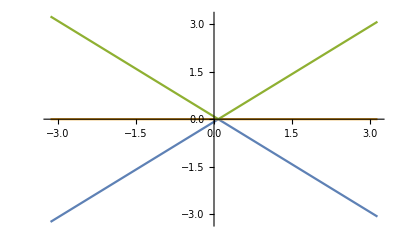

```mathematica
Plot[{Energies[0,0,k,Pi/6,2,0,1][[1]],Energies[0,0,k,Pi/6,2,0,1][[2]],Energies[0,0,k,Pi/6,2,0,1][[3]]},{k,-Pi,Pi}] (*phi=Pi/6*)
```

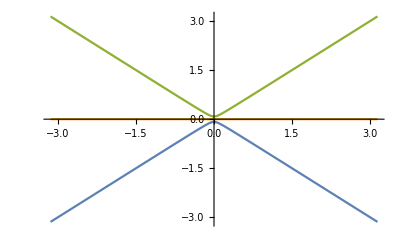

```mathematica
Plot[{Energies[0,0,k,0,2,0,1][[1]],Energies[0,0,k,0,2,0,1][[2]],Energies[0,0,k,0,2,0,1][[3]]},{k,-Pi,Pi}] (*phi=0*)
```

#### r=2 Case

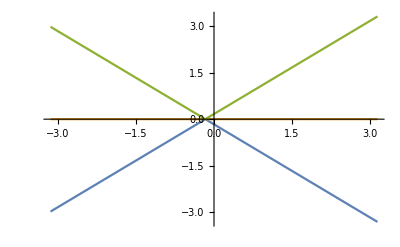

```mathematica
Plot[{Energies[0,0,k,Pi/6,2,0,2][[1]],Energies[0,0,k,Pi/6,2,0,2][[2]],Energies[0,0,k,Pi/6,2,0,2][[3]]},{k,-Pi,Pi}] (*phi=Pi/6*)
```

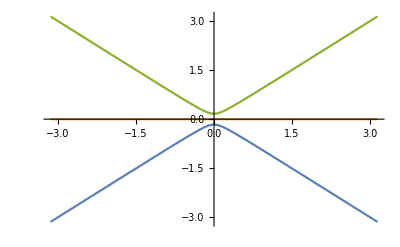

```mathematica
Plot[{Energies[0,0,k,0,2,0,2][[1]],Energies[0,0,k,0,2,0,2][[2]],Energies[0,0,k,0,2,0,2][[3]]},{k,-Pi,Pi}] (*phi=0*)
```

## Band-gap and Shift as a function of ϕ (and other parameters η, α, r)

```mathematica
Min[Table[Re[Energies[0,0,k,Pi/6,2,0,1][[3]]],{k,Range[-Pi,Pi,0.01]}]](*Min point of the upper band*)
```

0.00818277

```mathematica
Max[Table[Re[Energies[0,0,k,Pi/6,2,0,1][[1]]],{k,Range[-Pi,Pi,0.01]}]](*Max point of the lower band*)
```

-0.00818277

```mathematica
(*Thr difference between above two values, is actually the band-gap!!*)
```

The above minimum and maximum points of the bands are determined for ϕ = π/6, but we need to do the same thing for different ϕ’s in the range 0 to 2π.

Then do a plot.

```mathematica
(*Define a function for calculating bandgap along kz keeping kx=ky=0, ϕ, η, α and r are kept general*)
```

```mathematica
BandGap[phii_,eta_,al_,rr_]:=(Min[Table[Re[Energies[0,0,k,phii,eta,al,rr][[3]]],{k,Range[-Pi,Pi,0.01]}]]-Max[Table[Re[Energies[0,0,k,phii,eta,al,rr][[1]]],{k,Range[-Pi,Pi,0.01]}]]);
```

```mathematica
Shift[phii_,eta_,al_,rr_]:= Module[
{minPos,band,kList},
kList=Range[-Pi,Pi,0.01] (*range of kz*);
band =Table[Re[Energies[0,0,k,phii,eta,al,rr][[3]]],{k,kList}] (*the upper band for kx=ky=0 and varying kz*); 
minPos =Flatten[Position[band,Min[band]]] (*array-index of the minimum of the upper-band*);
kList[[minPos[[1]]]](*corresponding kz value*)
];
```

```mathematica
(*lets say at ϕ=0, η=2, α=0, r = 1, what is the bandgap and shift along kz keeping kx=ky=0 *)
```

```mathematica
BandGap[Pi/4,2,0,2]
```

0.235821

```mathematica
Shift[Pi/7,2,0,2]
```

-0.161593

### Cases, α = 0, η = 2 (In the following plots, the blue lines are the bandgap and yellow lines are the shifts)

```mathematica
phiList = Range[0,2Pi,0.01];
```

```mathematica
bandGapList = Table[BandGap[phi,2,0,1],{phi,phiList}];
shiftList = Table[Shift[phi,2,0,1],{phi,phiList}];
```

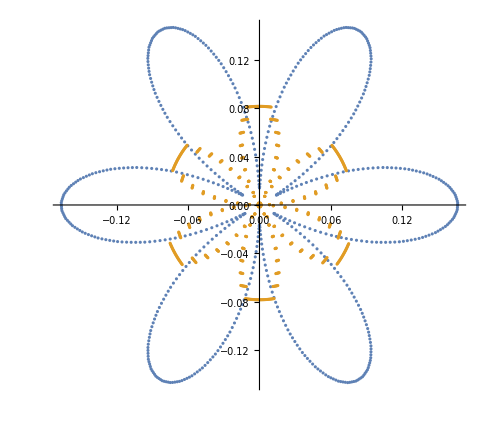

```mathematica
ListPolarPlot[{Transpose[{phiList,bandGapList}],Transpose[{phiList,Abs[shiftList]}]},AspectRatio->Automatic](*for r=1*)
```

```mathematica
bandGapList2 = Table[BandGap[phi,2,0,2],{phi,phiList}];
shiftList2 = Table[Shift[phi,2,0,2],{phi,phiList}];
```

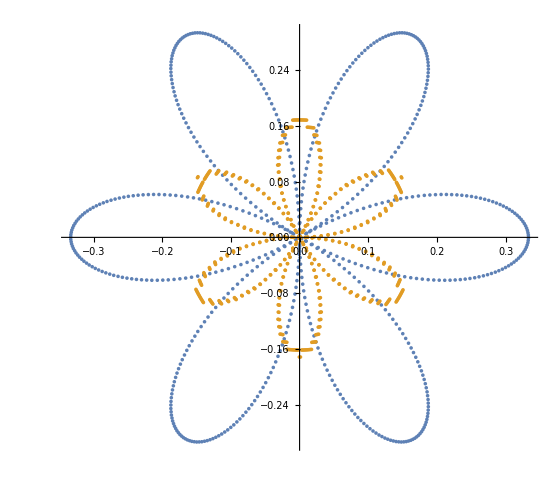

```mathematica
ListPolarPlot[{Transpose[{phiList,bandGapList2}],Transpose[{phiList,Abs[shiftList2]}]},AspectRatio->Automatic](*for r=2*)
```

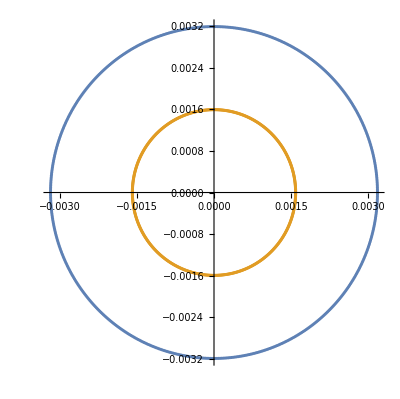

```mathematica
bandGapListSqrt2 = Table[BandGap[phi,2,0, Sqrt[2]],{phi,phiList}];
shiftListSqrt2 = Table[Shift[phi,2,0, Sqrt[2]],{phi,phiList}];

ListPolarPlot[{Transpose[{phiList,bandGapListSqrt2}],Transpose[{phiList,Abs[shiftListSqrt2]}]},AspectRatio->Automatic](*for r=Sqrt[2]*)
```

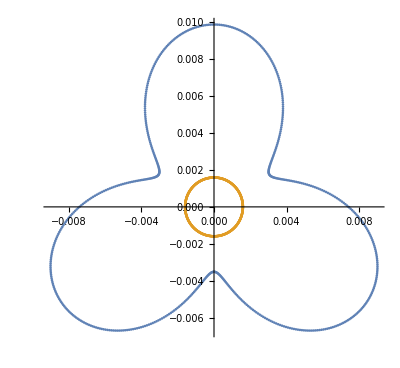

```mathematica
bandGapListNew1 = Table[BandGap[phi,2,0, 1.01Sqrt[2]],{phi,phiList}];
shiftListNew1 = Table[Shift[phi,2,0, 1.01Sqrt[2]],{phi,phiList}];
ListPolarPlot[{Transpose[{phiList,bandGapListNew1}],Transpose[{phiList,Abs[shiftListNew1]}]},AspectRatio->Automatic](*for r= 1.01 Sqrt[2]*)
```

```mathematica
bandGapListNew3 = Table[BandGap[phi,2,0, 2 (0.71)],{phi,phiList}];
shiftListNew3 = Table[Shift[phi,2,0, 2 (0.71)],{phi,phiList}];
ListPolarPlot[{Transpose[{phiList,bandGapListNew3}],Transpose[{phiList,shiftListNew3}]},AspectRatio->Automatic](*for r= 2(0.71)*)
```

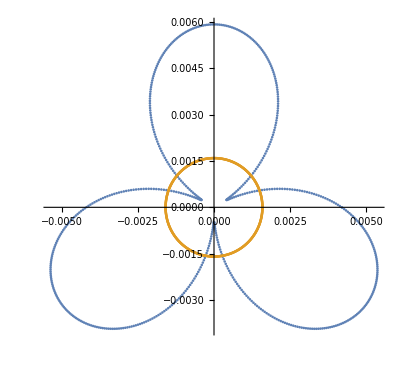

```mathematica
ListPolarPlot[{Transpose[{phiList,bandGapListNew3}],Transpose[{phiList,Abs[shiftListNew3]}]},AspectRatio->Automatic](*for r= 2(0.71)*)
```

```mathematica
bandGapListNew4 = Table[BandGap[phi,2,0, 2 (0.72)],{phi,phiList}];
shiftListNew4 = Table[Shift[phi,2,0, 2 (0.72)],{phi,phiList}];
ListPolarPlot[{Transpose[{phiList,bandGapListNew4}],Transpose[{phiList,shiftListNew4}]},AspectRatio->Automatic](*for r= 2(0.72)*)
```

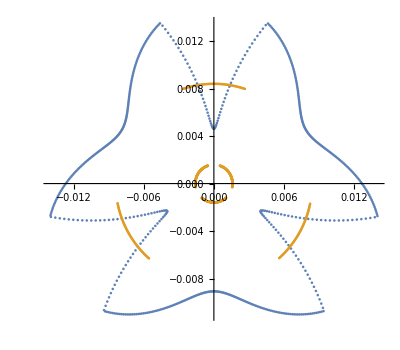

```mathematica
ListPolarPlot[{Transpose[{phiList,bandGapListNew4}],Transpose[{phiList,Abs[shiftListNew4]}]},AspectRatio->Automatic]
```

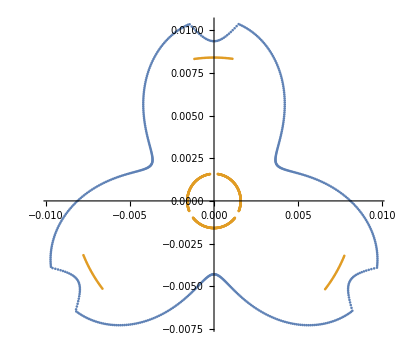

```mathematica
bandGapListNew5 = Table[BandGap[phi,2,0, 2 (0.715)],{phi,phiList}];
shiftListNew5 = Table[Shift[phi,2,0, 2 (0.715)],{phi,phiList}];

ListPolarPlot[{Transpose[{phiList,bandGapListNew5}],Transpose[{phiList,Abs[shiftListNew5]}]},AspectRatio->Automatic](*for r= 2(0.715)*)
```

## Some General Analysis of the Hamiltonian

```mathematica
Heff//FullSimplify//MatrixForm
```

(0 | ⅇ^(ⅈ phi) kx+(ⅈ ⅇ^(-2 ⅈ phi) kz (η-r Cos[α]))/(2 w η) | -(ⅇ^(2 ⅈ phi-ⅈ α) kz r-ⅇ^(ⅈ (2 phi+α)) kz r-4 ⅇ^(-ⅈ phi) ky w η)/(4 w η)
(ⅈ ⅇ^(2 ⅈ phi-ⅈ α) kz r+ⅈ ⅇ^(ⅈ (2 phi+α)) kz r-2 ⅈ ⅇ^(2 ⅈ phi) kz η+4 ⅇ^(-ⅈ phi) kx w η)/(4 w η) | 0 | (ⅇ^(-ⅈ (2 phi+α)) ((-1+ⅇ^(2 ⅈ α)) ky r+2 ⅇ^(ⅈ α) (ⅈ (r^2-η)+2 ⅇ^(3 ⅈ phi) kz w η)+2 kx (η-r Cos[α]) (-ⅈ Cos[α]+Sin[α])))/(4 w η)
(ⅇ^(-ⅈ (2 phi+α)) (-((-1+ⅇ^(2 ⅈ α)) kz r)+4 ⅇ^(ⅈ (3 phi+α)) ky w η))/(4 w η) | (ⅇ^(-ⅈ (phi+α)) (-ⅈ ⅇ^(3 ⅈ phi+2 ⅈ α) (kx-ⅈ ky) r+ⅇ^(3 ⅈ phi) (-ⅈ kx+ky) r+2 ⅇ^(ⅈ α) (2 kz w η+ⅈ ⅇ^(3 ⅈ phi) (-r^2+η+kx η))))/(4 w η) | 0)

```mathematica
Heff/.{kx->0,ky->0,α->0}//FullSimplify//MatrixForm
```

(0 | (ⅈ ⅇ^(-2 ⅈ phi) kz (-r+η))/(2 w η) | 0
(ⅈ ⅇ^(2 ⅈ phi) kz (r-η))/(2 w η) | 0 | ⅇ^(ⅈ phi) kz+(ⅈ ⅇ^(-2 ⅈ phi) (r^2-η))/(2 w η)
0 | ⅇ^(-ⅈ phi) kz+(ⅈ ⅇ^(2 ⅈ phi) (-r^2+η))/(2 w η) | 0)

```mathematica
Heff/.{kx->0,ky->0,α->Pi/2}//FullSimplify//MatrixForm
```

(0 | (ⅈ ⅇ^(-2 ⅈ phi) kz)/(2 w) | (ⅈ ⅇ^(2 ⅈ phi) kz r)/(2 w η)
-(ⅈ ⅇ^(2 ⅈ phi) kz)/(2 w) | 0 | ⅇ^(ⅈ phi) kz+(ⅈ ⅇ^(-2 ⅈ phi) (r^2-η))/(2 w η)
-(ⅈ ⅇ^(-2 ⅈ phi) kz r)/(2 w η) | ⅇ^(-ⅈ phi) kz-(ⅈ ⅇ^(2 ⅈ phi) (r^2-η))/(2 w η) | 0)

```mathematica
Heff/.{η->2,α->0}//FullSimplify//MatrixForm
```

(0 | ⅇ^(ⅈ phi) kx-(ⅈ ⅇ^(-2 ⅈ phi) kz (-2+r))/(4 w) | ⅇ^(-ⅈ phi) ky
ⅇ^(-ⅈ phi) kx+(ⅈ ⅇ^(2 ⅈ phi) kz (-2+r))/(4 w) | 0 | ⅇ^(ⅈ phi) kz+(ⅈ ⅇ^(-2 ⅈ phi) (-2+kx (-2+r)+r^2))/(4 w)
ⅇ^(ⅈ phi) ky | ⅇ^(-ⅈ phi) kz-(ⅈ ⅇ^(2 ⅈ phi) (-2+kx (-2+r)+r^2))/(4 w) | 0)

```mathematica
Heff/.{η->2,α->Pi/2}//FullSimplify//MatrixForm
```

(0 | ⅇ^(ⅈ phi) kx+(ⅈ ⅇ^(-2 ⅈ phi) kz)/(2 w) | ⅇ^(-ⅈ phi) ky+(ⅈ ⅇ^(2 ⅈ phi) kz r)/(4 w)
ⅇ^(-ⅈ phi) kx-(ⅈ ⅇ^(2 ⅈ phi) kz)/(2 w) | 0 | ⅇ^(ⅈ phi) kz-(ⅈ ⅇ^(-2 ⅈ phi) (2+2 kx-r (ky+r)))/(4 w)
ⅇ^(ⅈ phi) ky-(ⅈ ⅇ^(-2 ⅈ phi) kz r)/(4 w) | ⅇ^(-ⅈ phi) kz+(ⅈ ⅇ^(2 ⅈ phi) (2+2 kx-r (ky+r)))/(4 w) | 0)

```mathematica
Heff/.{η->2,α->0,kx->0,ky->0}//FullSimplify//MatrixForm
```

(0 | -(ⅈ ⅇ^(-2 ⅈ phi) kz (-2+r))/(4 w) | 0
(ⅈ ⅇ^(2 ⅈ phi) kz (-2+r))/(4 w) | 0 | ⅇ^(ⅈ phi) kz+(ⅈ ⅇ^(-2 ⅈ phi) (-2+r^2))/(4 w)
0 | ⅇ^(-ⅈ phi) kz-(ⅈ ⅇ^(2 ⅈ phi) (-2+r^2))/(4 w) | 0)

```mathematica
Heff/.{η->2,α->0,kx->0,ky->0,r->1}//FullSimplify//MatrixForm
```

(0 | (ⅈ ⅇ^(-2 ⅈ phi) kz)/(4 w) | 0
-(ⅈ ⅇ^(2 ⅈ phi) kz)/(4 w) | 0 | ⅇ^(ⅈ phi) kz-(ⅈ ⅇ^(-2 ⅈ phi))/(4 w)
0 | ⅇ^(-ⅈ phi) kz+(ⅈ ⅇ^(2 ⅈ phi))/(4 w) | 0)

```mathematica
Heff/.{η->2,α->0,kx->0,ky->0,r->2}//FullSimplify//MatrixForm
```

(0 | 0 | 0
0 | 0 | ⅇ^(ⅈ phi) kz+(ⅈ ⅇ^(-2 ⅈ phi))/(2 w)
0 | ⅇ^(-ⅈ phi) kz-(ⅈ ⅇ^(2 ⅈ phi))/(2 w) | 0)

```mathematica
Heff/.{η->2,α->0,kx->0,ky->0,r->Sqrt[2]}//FullSimplify//MatrixForm
```

(0 | -(ⅈ (-2+√2) ⅇ^(-2 ⅈ phi) kz)/(4 w) | 0
(ⅈ (-2+√2) ⅇ^(2 ⅈ phi) kz)/(4 w) | 0 | ⅇ^(ⅈ phi) kz
0 | ⅇ^(-ⅈ phi) kz | 0)

```mathematica
Heff/.{η->2,α->Pi/2,kx->0,ky->0}//FullSimplify//MatrixForm
```

(0 | (ⅈ ⅇ^(-2 ⅈ phi) kz)/(2 w) | (ⅈ ⅇ^(2 ⅈ phi) kz r)/(4 w)
-(ⅈ ⅇ^(2 ⅈ phi) kz)/(2 w) | 0 | ⅇ^(ⅈ phi) kz+(ⅈ ⅇ^(-2 ⅈ phi) (-2+r^2))/(4 w)
-(ⅈ ⅇ^(-2 ⅈ phi) kz r)/(4 w) | ⅇ^(-ⅈ phi) kz-(ⅈ ⅇ^(2 ⅈ phi) (-2+r^2))/(4 w) | 0)

```mathematica
Heff/.{η->2,α->Pi/2,kx->0,ky->0,r->1}//FullSimplify//MatrixForm
```

(0 | (ⅈ ⅇ^(-2 ⅈ phi) kz)/(2 w) | (ⅈ ⅇ^(2 ⅈ phi) kz)/(4 w)
-(ⅈ ⅇ^(2 ⅈ phi) kz)/(2 w) | 0 | ⅇ^(ⅈ phi) kz-(ⅈ ⅇ^(-2 ⅈ phi))/(4 w)
-(ⅈ ⅇ^(-2 ⅈ phi) kz)/(4 w) | ⅇ^(-ⅈ phi) kz+(ⅈ ⅇ^(2 ⅈ phi))/(4 w) | 0)

```mathematica
Heff/.{η->2,α->Pi/2,kx->0,ky->0,r->2}//FullSimplify//MatrixForm
```

(0 | (ⅈ ⅇ^(-2 ⅈ phi) kz)/(2 w) | (ⅈ ⅇ^(2 ⅈ phi) kz)/(2 w)
-(ⅈ ⅇ^(2 ⅈ phi) kz)/(2 w) | 0 | ⅇ^(ⅈ phi) kz+(ⅈ ⅇ^(-2 ⅈ phi))/(2 w)
-(ⅈ ⅇ^(-2 ⅈ phi) kz)/(2 w) | ⅇ^(-ⅈ phi) kz-(ⅈ ⅇ^(2 ⅈ phi))/(2 w) | 0)

```mathematica
Heff/.{η->2,α->Pi/2,kx->0,ky->0,r->Sqrt[2]}//FullSimplify//MatrixForm
```

(0 | (ⅈ ⅇ^(-2 ⅈ phi) kz)/(2 w) | (ⅈ ⅇ^(2 ⅈ phi) kz)/(2 √2 w)
-(ⅈ ⅇ^(2 ⅈ phi) kz)/(2 w) | 0 | ⅇ^(ⅈ phi) kz
-(ⅈ ⅇ^(-2 ⅈ phi) kz)/(2 √2 w) | ⅇ^(-ⅈ phi) kz | 0)

```mathematica
Range[-Pi,Pi,0.01][[2]]
```

-3.13159

```mathematica
Flatten[Position[Range[-Pi,Pi,0.01],%139]]
```

{2}

```mathematica
Abs[{-1,1}]
```

{1,1}

```mathematica
Abs[-1]
```

1